## gain profile of tweezer rf network at 5.63 W

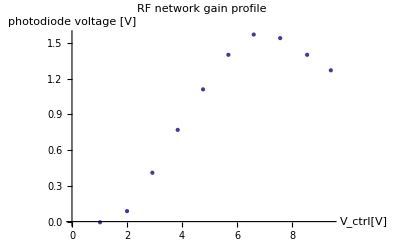

```mathematica
ctrl= {9.4,1.02,8.54,2.00,7.56,2.92,6.6,3.84,4.76,5.68};
pd={1.27,-.0054,1.4,.088,1.54,.41,1.57,.77,1.11,1.4};
data=Thread[{ctrl, pd}];
ListPlot[data,AxesLabel->{"V_ctrl[V]","photodiode voltage [V]"},PlotLabel->"RF network gain profile"]
```

## modulation

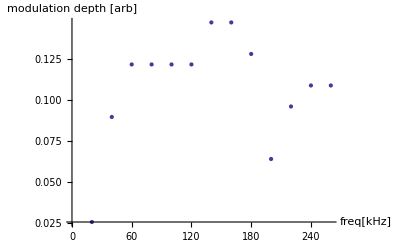

```mathematica
freq=Table[i, {i,20,260,20}];
amp={16,56,76,76,76,76,92,92,80,40,60,68,68}/624;
data=Thread[{freq,amp}];
ListPlot[data,AxesLabel->{"freq[kHz]","modulation depth [arb]"}]
```